## TemplateCircularHoneycombCover-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51h (15 June 2017)) loaded Sat 17 Jun 2017 09:30:53
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

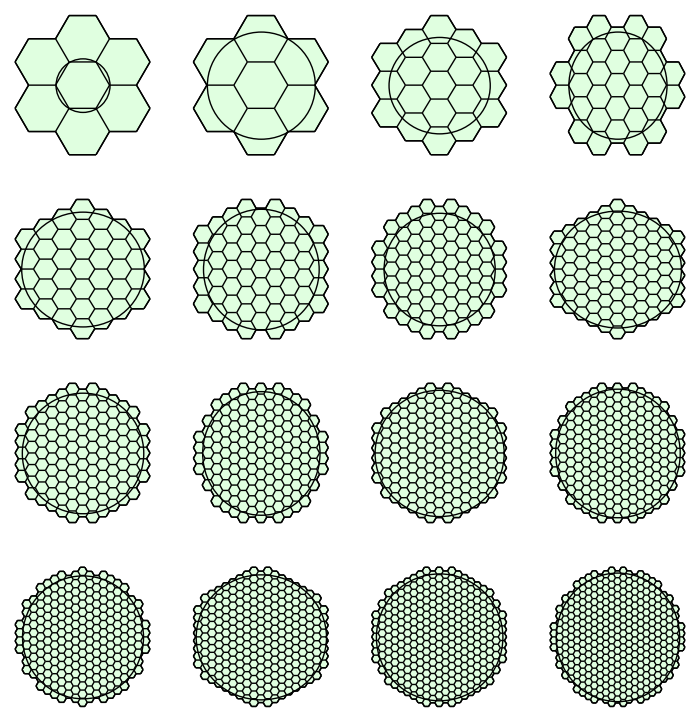

```mathematica
GraphicsGrid[Partition[ShowTissue[TemplateCircularHoneycombCover[#],Epilog-> Circle[{0,0},#]]&/@Range[16], 4],ImageSize-> 700]
```

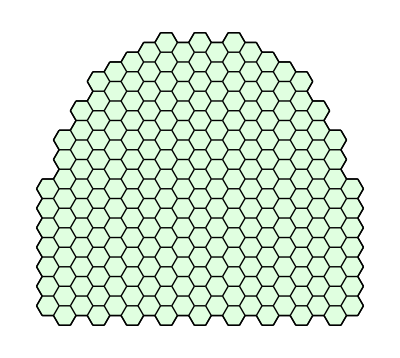

```mathematica
q=TemplateCircularHoneycombCover[12,25];
ShowTissue[q]
```